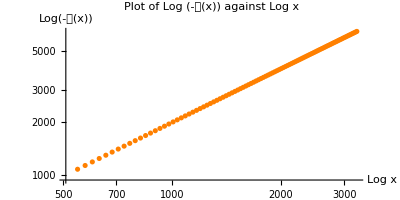

```mathematica
(*Define the prime counting function π(x) using an approximation*)PrimePiApprox[x_]:=If[x<2,0,Floor[x/Log[x]]]

(*Define the function G(x)*)
G[x_]:=Module[{e=Exp[1],logx,piX,piXDivE},logx=Log[x];
piX=PrimePiApprox[x];
piXDivE=PrimePiApprox[x/e];
piX^2-(e*x/logx)*piXDivE]

(*Define the range of x values*)
xMin=Exp[547];
xMax=Exp[3247];
xValues=Exp[Range[Log[xMin],Log[xMax],(Log[xMax]-Log[xMin])/100]];

(*Compute G(x) and its negative log*)
gValues=G/@xValues;
logNegGValues=Log[Abs[-gValues]];

(*Plot the graph*)
ListLogLogPlot[Transpose[{Log[xValues],logNegGValues}],PlotStyle->Orange,AxesLabel->{"Log x","Log(-𝒢(x))"},PlotLabel->"Plot of Log (-𝒢(x)) against Log x",GridLines->None,AspectRatio->1/2]
```

```mathematica
Show[%26,AxesStyle->Black]
```

-Graphics-

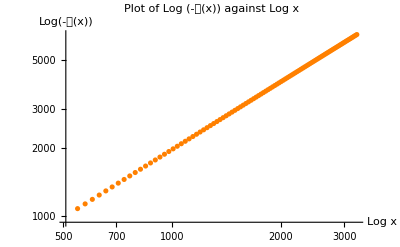

```mathematica
Show[%27,AspectRatio->1/GoldenRatio]
```